### Graph Visualization

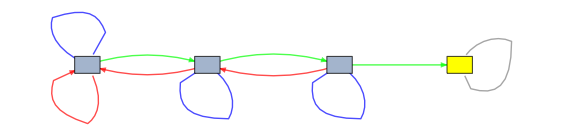

```mathematica
greenEdges={
{0,0,0,0},
{1,0,0,0},
{0,1,0,0},
{0,0,1,1}
} ;

blueEdges={{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};

redEdges = {
{0,0,0,0},
{0,0,1,0},
{0,0,0,1},
{0,0,0,1}
};

grayEdges = {
{1,0,0,0},
{0,0,0,0},
{0,0,0,0},
{0,0,0,0}
};

greenGraph=AdjacencyGraph[greenEdges];
blueGraph=AdjacencyGraph[blueEdges];
redGraph=AdjacencyGraph[redEdges];
grayGraph=AdjacencyGraph[grayEdges];

combinedGraph=GraphUnion[greenGraph,blueGraph,redGraph, grayGraph];

edgeColors=Join[
Thread[EdgeList[greenGraph]->Green],
Thread[EdgeList[blueGraph]->Blue],
Thread[EdgeList[redGraph]->Red],
Thread[EdgeList[grayGraph]->Gray]

];

Graph[combinedGraph,EdgeStyle->edgeColors,ImagePadding->20, VertexShapeFunction->"Rectangle", VertexSize->Medium, VertexStyle->{1->Yellow}]
```

### Model definition

```mathematica
m := Subscript[λ, 3]{
{0,0,0,0},
{1,0,0,0},
{0,1,0,0},
{0,0,1,1}
} +Subscript[λ, 2]{
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}
}+Subscript[λ, 1]{
{1,1,0,0},
{0,0,1,0},
{0,0,0,0},
{0,0,0,1}
}
```

```mathematica
Subscript[λ, 1]({{1, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})+ Subscript[λ, 2]({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})+Subscript[λ, 3]({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 1}})
```

```mathematica
m//MatrixForm
```

(λ_1+λ_2 | λ_1 | 0 | 0
λ_3 | λ_2 | λ_1 | 0
0 | λ_3 | λ_2 | 0
0 | 0 | λ_3 | λ_1+λ_2+λ_3)

#### BoxState defines a Markov chain where m is the transition matrix

```mathematica
boxState[a_, b_, c_, n_] :=MatrixPower[m/.{Subscript[λ, 1]->a, Subscript[λ, 2]->b, Subscript[λ, 3]->c}, n] . {1,0,0,0}
```

### Simulation

Assume the user hits “Hard” a 20% of the time, “Okay” 10%, and “Good” 70%.

What is the distribution of cards after 3 reviews? How about 7?

```mathematica
Grid@Table[{i,MatrixForm@ boxState[.2,.1,.7, i]}, {i, {3, 5, 7, 21}}]
```

3 | (0.125
0.287
0.245
0.343)
5 | (0.06151
0.12803
0.13818
0.67228)
7 | (0.0299169
0.0598787
0.0687911
0.841413)
21 | (0.00017644
0.000346447
0.000409159
0.999068)

What is the steady state?

```mathematica
A := m/.{Subscript[λ, 1]->.2, Subscript[λ, 2]->.1, Subscript[λ, 3]->.7}
Det[A]
```

-0.053

The matrix is regular since its determinant is nonzero.

```mathematica
ia = IdentityMatrix[4] -  A;
ia // MatrixForm
```

(0.7 | -0.2 | 0 | 0
-0.7 | 0.9 | -0.2 | 0
0 | -0.7 | 0.9 | 0
0 | 0 | -0.7 | 0.)

The vector {0, 0, 0, 1} satisfies the system, so it is the steady state.

```mathematica
Grid@Table[{i,MatrixForm@ boxState[.9,.05,.05, i]}, {i, {1000000}}]
```

1000000 | (1.35987×10^-60
7.53403×10^-62
3.96586×10^-63
1.)